# Pentagon

### Author

Eric W. Weisstein
July 3, 2018

This notebook downloaded from http://mathworld.wolfram.com/notebooks/Polygons/Pentagon.nb.

For more information, see Eric's MathWorld entry http://mathworld.wolfram.com/Pentagon.html.

©2018 Wolfram Research, Inc. except for portions noted otherwise

## Examples

```mathematica
laminae=Select[EntityList[EntityClass["Lamina","Polygon"]],#["VertexCount"]==5&]
```

{isosceles pentagon,isosceles right pentagon,regular pentagon}

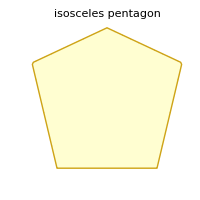
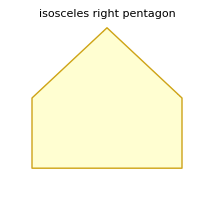
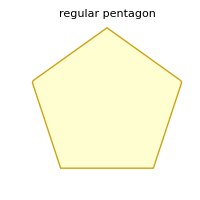

```mathematica
Show[#,PlotLabel->#2]&@@@EntityValue[laminae,{"Graphics","Name"}]
```

```mathematica
EntityValue[laminae,"VariablePlotDefaults"]
```

{Missing[UnknownProperty,{Lamina,VariablePlotDefaults}],Missing[UnknownProperty,{Lamina,VariablePlotDefaults}],Missing[UnknownProperty,{Lamina,VariablePlotDefaults}]}

## Figure

```mathematica
polys={
Polygon[Entity["Lamina","FilledIsoscelesPentagon"]["Vertices"][2,1.5,1.5,2]]->"isosceles pentagon",
Polygon[Entity["Lamina","FilledIsoscelesRightPentagon"]["Vertices"][2,1,1.5]]->"isosceles right pentagon",
Polygon[Entity["Lamina","FilledRegularPentagon"]["Vertices"][1]]->"regular pentagon"
};
```

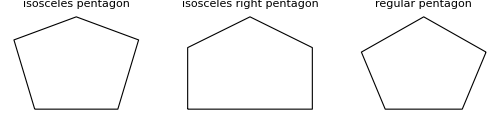

```mathematica
GraphicsGrid[Partition[
Graphics[{EdgeForm[Black],FaceForm[None],#},PlotLabel->Style[TextCell[#2,PageWidth->100,TextAlignment->Center],Directive[Italic,FontFamily->"Times"]]]&@@@polys,UpTo[3]],Spacings->50,ImageSize->500]
```